# Diagnostic Performance vs Latent Dimension

## Parameters regression

This notebook summarizes diagonal-test performance for ENCA models trained with different latent-space dimensions. For each z dimension, the diagnostic output provides the Pearson correlation and normalized RMSE for each physical parameter. The plots compare correlation with a baseline-corrected performance score, using the prior-mean predictor as the zero-performance reference.

The numerical pairs below are copied from the output of diag_test.py. For each parameter and latent dimension, the first number is the Pearson correlation between true and predicted parameter values, and the second number is RMSE divided by the prior range, reported in percent.

```mathematica
τ5={0.9353,10.8};
T5={0.9510,9.3};
Nd5={0.9121,13.1};
σ5={0.9146,11.8};
Bmax5={0.9733,7.8};
```

```mathematica
τ5cpu={0.9302,10.6};
T5cpu={0.9334,10.7};
Nd5cpu={0.3801,27.0};
σ5cpu={0.8997,12.8};
Bmax5cpu={0.9088,12.3};
```

```mathematica
τ6={0.9776,6.1};
T6={0.8528,15.4};
Nd6={0.4464,26.0};
σ6={0.0035,29.3};
Bmax6={0.9367,10.0};
```

```mathematica
τ6cpu={0.9799,5.7};
T6cpu={0.8537,15.4};
Nd6cpu={0.4677,25.5};
σ6cpu={0.0035,29.3};
Bmax6cpu={0.9505,8.9};
```

```mathematica
τ7={0.9832,5.4};
T7={0.9827,5.5};
Nd7={0.9479,9.3};
σ7={-0.0468,29.5};
Bmax7={0.9804,5.9};
```

```mathematica
τ7cpu={0.9816,5.5};
T7cpu={0.9780,6.2};
Nd7cpu={0.9611,7.9};
σ7cpu={0.9099,12.1};
Bmax7cpu={0.9822,5.7};
```

```mathematica
τ8={0.9826,5.4};
T8={0.9658,7.7};
Nd8={0.8997,12.5};
σ8={0.0195,29.2};
Bmax8={0.9668,7.3};
```

```mathematica
τ9={0.9886,4.3};
T9={0.9802,5.9};
Nd9={0.9570,8.8};
σ9={0.4811,25.6};
Bmax9={0.9841,5.2};
```

```mathematica
τ9cpu={0.9912,3.8};
T9cpu={0.9870,4.7};
Nd9cpu={0.9635,7.7};
σ9cpu={-0.0099,29.3};
Bmax9cpu={0.9872,4.6};
```

```mathematica
τ10={0.9847,5.0};
T10={0.9861,4.9};
Nd10={0.9393,10.0};
σ10={-0.0034,29.4};
Bmax10={0.9869,4.6};
```

```mathematica
τ11cpu={0.9883,4.4};
T11cpu={0.9873,4.7};
Nd11cpu={0.9535,8.8};
σ11cpu={0.0413,29.2};
Bmax11cpu={0.9876,4.5};
```

```mathematica
τ12={0.9882,4.4};
T12={0.9841,5.4};
Nd12={0.9388,10.2};
σ12={0.0493,29.2};
Bmax12={0.9896,4.6};
```

```mathematica
τ12cpu={0.9914,3.8};
T12cpu={0.9888,4.4};
Nd12cpu={0.9507,9.1};
σ12cpu={0.0277,29.2};
Bmax12cpu={0.9894,4.2};
```

```mathematica
τ13cpu={0.9872,4.6};
T13cpu={0.9862,4.9};
Nd13cpu={0.9347,10.2};
σ13cpu={-0.0295,29.4};
Bmax13cpu={0.9903,4.0};
```

```mathematica
τ14={0.9907,3.9};
T14={0.9896,4.3};
Nd14={0.9638,7.6};
σ14={0.0044,29.3};
Bmax14={0.9910,3.8};
```

```mathematica
τ14cpu={0.9926,3.5};
T14cpu={0.9924,3.6};
Nd14cpu={0.9644,7.7};
σ14cpu={-0.0433,29.4};
Bmax14cpu={0.9916,3.7};
```

```mathematica
τ15cpu={0.9928,3.4};
T15cpu={0.9926,3.6};
Nd15cpu={0.9711,6.8};
σ15cpu={0.0031,29.3};
Bmax15cpu={0.9911,3.8};
```

```mathematica
(* training: 20260521_enca_z16_3*)
τ16={0.9891,4.3};
T16={0.9857,5.0};
Nd16={0.9610,7.9};
σ16={-0.0579,29.5};
Bmax16={0.9848,5.0};
```

```mathematica
(*training 20260527_enca_z16b_3*)
τ16b={0.9926,3.5};
T16b={0.9897,4.2};
Nd16b={0.9662,7.4};
σ16b={-0.0223,29.5};
Bmax16b={0.9933,3.3};
```

```mathematica
τ16cpu={0.9867,4.7};
T16cpu={0.9861,4.9};
Nd16cpu={0.9618,7.9};
σ16cpu={0.0136,29.3};
Bmax16cpu={0.9874,4.6};
```

```mathematica
τ18={0.9947,2.9};
T18={0.9872,4.7};
Nd18={0.9663,7.4};
σ18={0.0084,29.3};
Bmax18={0.9901,4.0};
```

```mathematica
zDims={5,6,7,8,9,10,12,14,16,16,18};
zDimsCPU={5,6,7,9,11,12,13,14,15,16};
```

```mathematica
paramData=<|"τ"->{τ5,τ6,τ7,τ8,τ9,τ10,τ12,τ14,τ16,τ16b,τ18},"T"->{T5,T6,T7,T8,T9,T10,T12,T14,T16,T16b,T18},"Nd"->{Nd5,Nd6,Nd7,Nd8,Nd9,Nd10,Nd12,Nd14,Nd16,Nd16b,Nd18},"σ"->{σ5,σ6,σ7,σ8,σ9,σ10,σ12,σ14,σ16,σ16b,σ18},"Bmax"->{Bmax5,Bmax6,Bmax7,Bmax8,Bmax9,Bmax10,Bmax12,Bmax14,Bmax16,Bmax16b,Bmax18}|>;
```

```mathematica
paramDataCPU=<|"τ"->{τ5cpu,τ6cpu,τ7cpu,τ9cpu,τ11cpu,τ12cpu,τ13cpu,τ14cpu,τ15cpu,τ16cpu},"T"->{T5cpu,T6cpu,T7cpu,T9cpu,T11cpu,T12cpu,T13cpu,T14cpu,T15cpu,T16cpu},"Nd"->{Nd5cpu,Nd6cpu,Nd7cpu,Nd9cpu,Nd11cpu,Nd12cpu,Nd13cpu,Nd14cpu,Nd15cpu,Nd16cpu},"σ"->{σ5cpu,σ6cpu,σ7cpu,σ9cpu,σ11cpu,σ12cpu,σ13cpu,σ14cpu,σ15cpu,σ16cpu},"Bmax"->{Bmax5cpu,Bmax6cpu,Bmax7cpu,Bmax9cpu,Bmax11cpu,Bmax12cpu,Bmax13cpu,Bmax14cpu,Bmax15cpu,Bmax16cpu}|>;
```

```mathematica
corr[param_]:=paramData[param][[All,1]];

baselineError=1/Sqrt[12];
perf[param_]:=1-(paramData[param][[All,2]]/100)/baselineError;
```

Performance score 
For each physical parameter, the diagnostic test reports 
normalized RMSE=RMSE/prior range.
Since the parameters are sampled uniformly from their prior intervals, a trivial baseline predictor is one that always predicts the prior mean, i.e. the midpoint of the allowed interval.
For a uniform distribution on[a,b], the standard deviation is (b-a)/Sqrt[12].
Therefore,the normalized RMSE of this trivial mean predictor is 
baselineError=((b-a)/Sqrt[12])/(b-a)=1/Sqrt[12].
We define the baseline-corrected performance score as 
performance=1-normalizedRMSE/baselineError=1-(RMSE/prior range)/(1/Sqrt[12]).

Interpretation:
performance=1  --- perfect prediction,RMSE=0 
performance=0  --- no better than always predicting the prior mean 
performance<0 ---  worse than the prior-mean predictor 

Thus this score measures the fraction of the naive baseline error removed by the encoder.
For example, performance=0.6 means that the model has reduced the RMSE by about 60% relative to always predicting the prior mean.

```mathematica
dualAxisPlot[title_,corrVals_,perfVals_]:=Module[{perfData,corrData,gridZDims},
perfData=Transpose[{zDims,perfVals}];
corrData=Transpose[{zDims,corrVals}];
gridZDims=Range[Min[zDims],Max[zDims]];
ListLinePlot[{perfData,corrData},
Frame->True,Axes->False,
PlotMarkers->{Automatic,16},
PlotStyle->{Blue,Darker[Red]},PlotLegends->Placed[{"1 - (mean) normalized RMSE","mean corr"},Above],FrameLabel->{"latent dimension z","performance score",None,"correlation"},FrameTicks->{{Automatic,Automatic},{Thread[{zDims,zDims}],None}},PlotRange->{{Min[zDims]-1,Max[zDims]+1},{-0.05,1.02}},GridLines->{gridZDims,Automatic},
FrameStyle->Directive[Black,AbsoluteThickness[1.6]],
FrameTicksStyle->Directive[Black,14],
LabelStyle->Directive[Black,16],
ImageSize->620,
PlotLabel->Style[title,17,Black]]]
```

```mathematica
corrCPU[param_] := paramDataCPU[param][[All, 1]];
perfCPU[param_] := 1 - ((paramDataCPU[param][[All, 2]]/100)/baselineError);

cpuSeriesFor[corrVals_, perfVals_] := Module[{param},
  param = SelectFirst[
    Keys[paramData],
    corr[#] === corrVals && perf[#] === perfVals &,
    None
  ];
  If[param =!= None,
    {corrCPU[param], perfCPU[param]},
    If[
      ValueQ[paramsNoSigma] && corrVals === meanCorrNoSigma &&
        perfVals === meanPerfNoSigma,
      {
        Mean /@ Transpose[corrCPU /@ paramsNoSigma],
        Mean /@ Transpose[perfCPU /@ paramsNoSigma]
      },
      {{}, {}}
    ]
  ]
];

dualAxisPlot[title_, corrVals_, perfVals_] := Module[
  {perfData, corrData, cpuCorrVals, cpuPerfVals, perfDataCPU, corrDataCPU,
   plotData, plotStyles, plotMarkers, plotLegends, allZDims, gridZDims},
  perfData = Transpose[{zDims, perfVals}];
  corrData = Transpose[{zDims, corrVals}];
  {cpuCorrVals, cpuPerfVals} = cpuSeriesFor[corrVals, perfVals];
  perfDataCPU = If[cpuPerfVals === {}, {}, Transpose[{zDimsCPU, cpuPerfVals}]];
  corrDataCPU = If[cpuCorrVals === {}, {}, Transpose[{zDimsCPU, cpuCorrVals}]];
  plotData = DeleteCases[{perfData, corrData, perfDataCPU, corrDataCPU}, {}];
  plotStyles = Take[
    {Blue, Darker[Red], Directive[Blue, Dashed], Directive[Darker[Red], Dashed]},
    Length[plotData]
  ];
  plotMarkers = Take[
    {{"●", 16}, {"■", 16}, {"○", 16},
     {"□", 16}},
    Length[plotData]
  ];
  plotLegends = Take[
    {"1 - (mean) normalized RMSE", "mean corr",
     "CPU 1 - (mean) normalized RMSE", "CPU mean corr"},
    Length[plotData]
  ];
  allZDims = Sort[Union[zDims, If[cpuCorrVals === {}, {}, zDimsCPU]]];
  gridZDims = Range[Min[allZDims], Max[allZDims]];
  ListLinePlot[
    plotData,
    Frame -> True,
    Axes -> False,
    PlotMarkers -> plotMarkers,
    PlotStyle -> plotStyles,
    PlotLegends -> Placed[plotLegends, Above],
    FrameLabel -> {"latent dimension z", "performance score", None,
      "correlation"},
    FrameTicks -> {{Automatic, Automatic}, {Thread[{allZDims, allZDims}], None}},
    PlotRange -> {{Min[allZDims] - 1, Max[allZDims] + 1}, {-0.05, 1.02}},
    GridLines -> {gridZDims, Automatic},
    FrameStyle -> Directive[Black, AbsoluteThickness[1.6]],
    FrameTicksStyle -> Directive[Black, 14],
    LabelStyle -> Directive[Black, 16],
    ImageSize -> 620,
    PlotLabel -> Style[title, 17, Black]
  ]
]
```

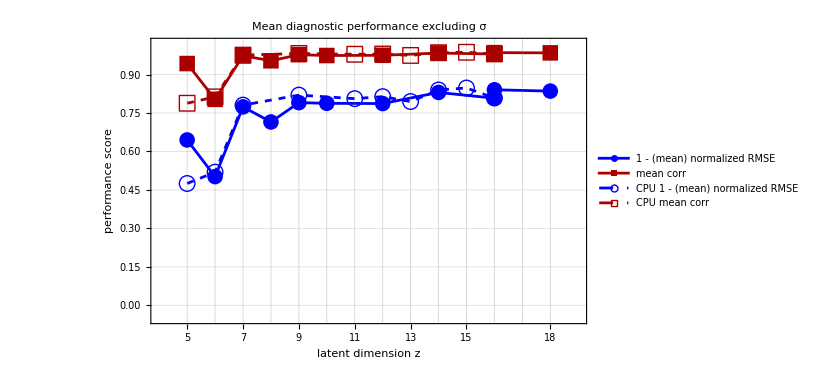

```mathematica
paramsNoSigma={"τ","T","Nd","Bmax"};

meanCorrNoSigma=Mean/@Transpose[corr/@paramsNoSigma];
meanPerfNoSigma=Mean/@Transpose[perf/@paramsNoSigma];

dualAxisPlot["Mean diagnostic performance excluding σ",meanCorrNoSigma,meanPerfNoSigma]
```

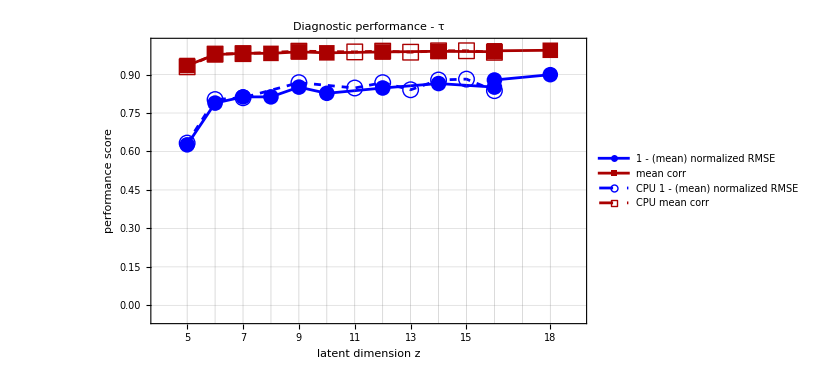

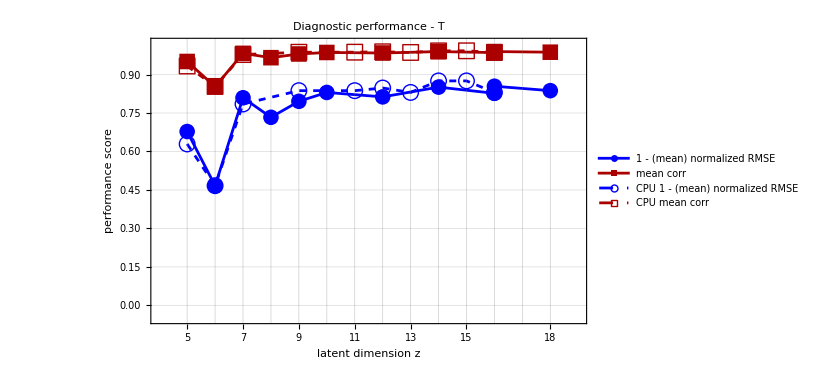

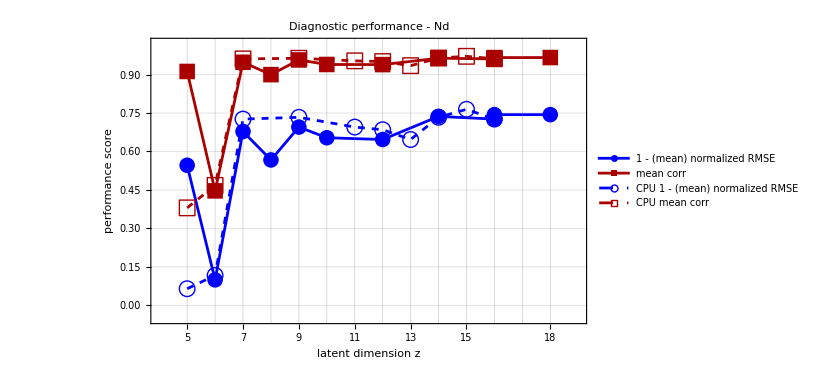

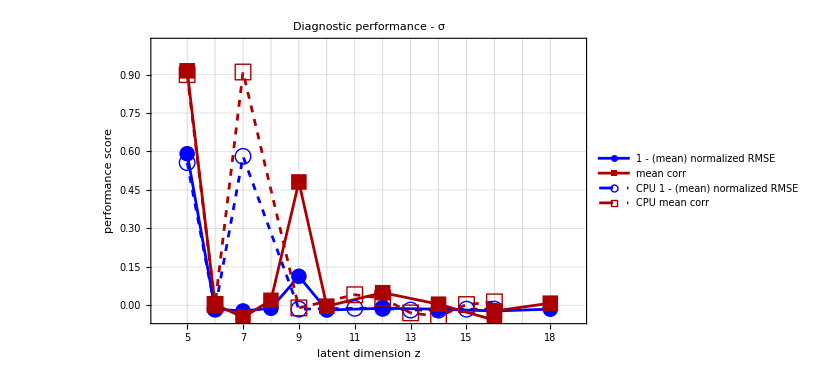

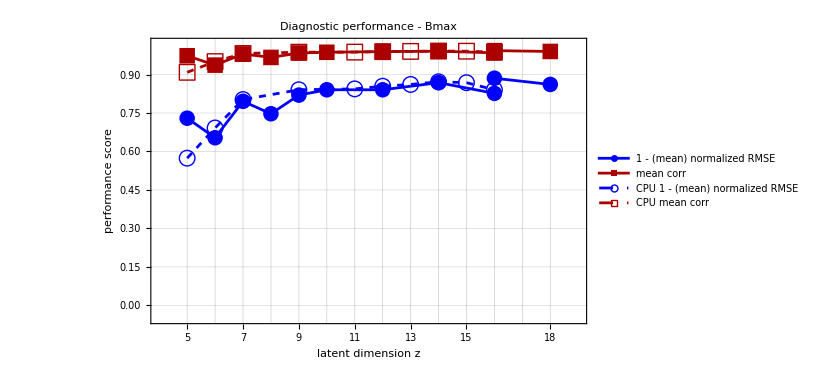

```mathematica
dualAxisPlot["Diagnostic performance - τ",corr["τ"],perf["τ"]]
dualAxisPlot["Diagnostic performance - T",corr["T"],perf["T"]]
dualAxisPlot["Diagnostic performance - Nd",corr["Nd"],perf["Nd"]]
dualAxisPlot["Diagnostic performance - σ",corr["σ"],perf["σ"]]
dualAxisPlot["Diagnostic performance - Bmax",corr["Bmax"],perf["Bmax"]]
```

## Reconstruction

Parameters : tau = 5, T = 6, Nd = 12, sigma = 0.02, Bmax = 8
nseeds = 10

Reconstruction performance
The reconstruction tests are run with the same physical parameters and the same number of noise realizations for each latent dimension, so the reported mean_RMSE values from recon_test.py are directly comparable. Lower mean_RMSE means better reconstruction.

To plot a higher-is-better score, the RMSE values are normalized by the worst RMSE among the currently tested latent dimensions:

reconstruction performance = 1 - meanRMSE/rmseRef,

where rmseRef = Max[Join[meanRMSE, meanRMSEcpu]]. With this definition, performance = 1 would correspond to perfect reconstruction, while performance = 0 corresponds to the worst model in the current comparison set. For example, a value of 0.47 means that the model reduces the reconstruction RMSE by about 47% relative to the current worst model.

```mathematica
zdim={5,6,7,8,9,10,12,14,16,16,18};
meanRMSE={111.62,84.7185,46.3609,45.0629,67.978,51.158,48.7618,57.3424,66.584,47.538,34.693};
```

```mathematica
zdimCPU={5,6,7,9,11,12,13,14,15,16};
meanRMSEcpu={107.729,46.2388,126.544,41.4994,49.7207,40.5402,53.6159,35.1991,36.1268,33.6649};
```

```mathematica
rmseRef=Max[Join[meanRMSE,meanRMSEcpu]];
reconPerf=1-meanRMSE/rmseRef;
reconPerfCPU=1-meanRMSEcpu/rmseRef;
```

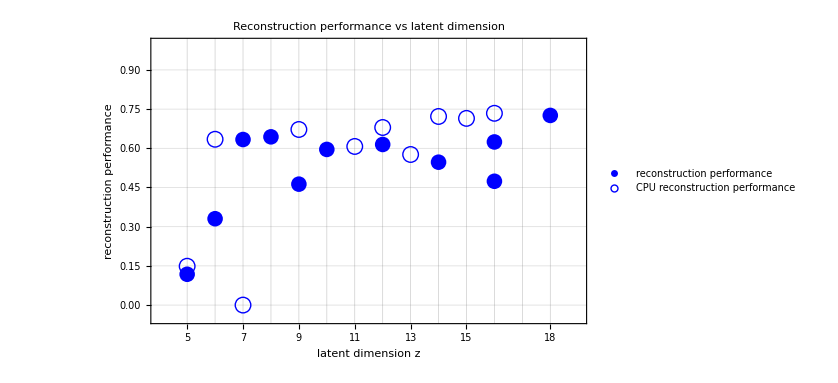

```mathematica
reconZDimsAll = Sort[Union[zdim, zdimCPU]];

reconGridZDims = Range[Min[reconZDimsAll], Max[reconZDimsAll]];
ListPlot[
  {
    Transpose[{zdim, reconPerf}],
    Transpose[{zdimCPU, reconPerfCPU}]
  },
  Frame -> True,
  Axes -> False,
  PlotMarkers -> {{"●", 16}, {"○", 16}},
  PlotStyle -> {Blue, Directive[Blue, Dashed]},
  PlotLegends -> Placed[{"reconstruction performance",
    "CPU reconstruction performance"}, Above],
  FrameLabel -> {"latent dimension z", "reconstruction performance"},
  PlotLabel -> Style["Reconstruction performance vs latent dimension", 17, Black],
  FrameTicks -> {{Automatic, Automatic}, {Thread[{reconZDimsAll, reconZDimsAll}],
    None}},
  GridLines -> {reconGridZDims, Automatic},
  PlotRange -> {{Min[reconZDimsAll] - 1, Max[reconZDimsAll] + 1}, {-0.05, 1}},
  FrameStyle -> Directive[Black, AbsoluteThickness[1.6]],
  FrameTicksStyle -> Directive[Black, 14],
  LabelStyle -> Directive[Black, 16],
  ImageSize -> 620
]
```